## N = 100

## Data

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
datasets = {"Strength","Connectivity","Universality","Noise","Rewiring","Multistability"};
type = {"train","test"};
reps = Range[0,9];
pars = Range[0,2];
```

```mathematica
σ = {.1,.15,.2};
Cn = {0.5,0.75,1};
η = {0.1,1,2}*σ⟦-1⟧;
ϵ = {.001,.01,.025};
ρ = {.01,.1,.25};
μ = {.05,.25,.5};
```

```mathematica
{{sTrn,sTst},{cTrn,cTst},{uTrn,uTst},{nTrn,nTst},{rTrn,rTst},{mTrn,mTst}} = Table[Table[Flatten@Import["../Results/Synthetic/100/"<>datasets⟦d⟧<>"/loss_percentage/"<>t<>"_"<>ToString@i<>ToString@j<>".csv"],{t,type},{i,pars},{j,reps}],{d,1,Length[datasets]}];
{{sTrnE,sTstE},{cTrnE,cTstE},{uTrnE,uTstE},{nTrnE,nTstE},{rTrnE,rTstE},{mTrnE,mTstE}} = Table[Table[Flatten@Import["../Results/Synthetic/100/"<>datasets⟦d⟧<>"/loss_epochs/"<>t<>"_"<>ToString@i<>ToString@j<>".csv"],{t,type},{i,pars},{j,reps}],{d,1,Length[datasets]}];
{{sTrnN,sTstN},{cTrnN,cTstN},{uTrnN,uTstN},{nTrnN,nTstN},{rTrnN,rTstN},{mTrnN,mTstN}} = Table[Table[Flatten@Import["../Results/Synthetic/100/"<>datasets⟦d⟧<>"/loss_percentage_null/"<>t<>"_"<>ToString@i<>ToString@j<>".csv"],{t,type},{i,pars},{j,reps}],{d,1,Length[datasets]}];
```

```mathematica
ErrorLogPlot[d_,leg_]:=Module[{data,error,max,min,pts},
	data = Mean/@d;
	error = StandardError/@d;
	max = data + error;
	min = data - error;
	pts = Thread[{ticks,#}]&/@data;
	max = Thread[{ticks,#}]&/@max;
	min = Thread[{ticks,#}]&/@min;
	Show[
		ListLogLogPlot[Flatten[Thread[{min,max}],1],Joined->True,
					Filling->Table[i -> {i+1},{i,1,2Length[data],2}],
					FillingStyle->LightGray,
					Frame->True,
					FrameTicks->{{All,None},{All,None}}, 
					FrameTicksStyle->16,
					FrameLabel->{"|D/N|","prediction error"},
					PlotStyle->Opacity[0]
					],
		ListLogLogPlot[pts,Joined->True,Frame->True,
					PlotLegends->SwatchLegend[leg,LegendMarkers->"Bubble",LegendLayout->"ReversedColumn"]],
		ListLogLogPlot[pts,PlotStyle->Directive[Thick, PointSize->0.02],Frame->True],
		ListLogLogPlot[pts,PlotStyle->Directive[Thick, White, PointSize->0.01],Frame->True]
		]
]
```

```mathematica
StandardError[x_]:= StandardDeviation[x]/(√Length[x])
ticks = {.01,.10,.25,.50,.75,1.00}*3;
```

## Loss Epochs

```mathematica
epochsPlot[dtrn_,dtst_,par_,p_,title_]:=ListLogPlot[{
		Mean@dtrn⟦1,All⟧,Mean@dtrn⟦2,All⟧,Mean@dtrn⟦3,All⟧,
		Mean@dtst⟦1,All⟧,Mean@dtst⟦2,All⟧,Mean@dtst⟦3,All⟧},
		Frame->True,Joined->True,FrameTicks->{{Automatic,None},{Automatic,None}},PlotRange->{0.006,0.3},
		PlotStyle->{
			Directive@{ColorData[98][1],Opacity[0.6],Thickness[0.01]},
			Directive@{ColorData[98][1],Opacity[0.6],Thickness[0.01],Dashed},
			Directive@{ColorData[98][1],Opacity[0.6],Thickness[0.01],Dotted},
			Directive@{ColorData[98][2],Opacity[0.6],Thickness[0.01]},
			Directive@{ColorData[98][2],Opacity[0.6],Thickness[0.01],Dashed},
			Directive@{ColorData[98][2],Opacity[0.6],Thickness[0.01],Dotted}
			},
		FrameLabel->{{"prediction error",None},{"epochs",Style[title,14]}},
		PlotLegends->{
			Placed[LineLegend[Directive/@{{Black},{Black,Dashed},{Black,Dotted}},par,LegendLayout->"ReversedColumn",LegendLabel->Style[p,Bold,14],LegendFunction->"Frame"],Right],
			Placed[SwatchLegend[{ColorData[98][1],ColorData[98][2]},{"train","test"},LegendLayout->"ReversedColumn"],Right]
		}
	]
```

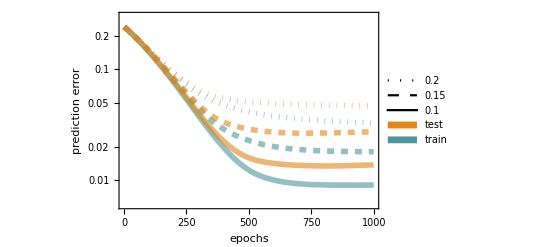

```mathematica
epochsPlot[sTrnE,sTstE,σ,"σ","interaction strength"]
```

## Percentage loss

```mathematica
blue=RGBColor[17.6/100,41.6/100,63.1/100];
green=RGBColor[34.9/100,66.7/100,33.3/100];
yellow=RGBColor[96.9/100,68.6/100,20.8/100];
red=RGBColor[86.3/100,13.3/100,19.6/100];
purple=RGBColor[55.3/100,27.5/100,55.7/100];
grey=RGBColor[55.7/100,57.3/100,56.9/100];
apple6={blue,green,yellow,red,purple,grey};
```

```mathematica
percentagesPlot[d_,leg_,p_,title_]:=Module[{min,max,p1,p2,p3,p4,p5,p6,p7,p8,p9,p10,p11,p12},
	p1 = ListLogLogPlot[Thread[{ticks,#}]&/@d⟦1,All⟧,Joined->True,PlotStyle->Directive@{blue,Opacity[0.4],Thickness[0.005]},PlotRange->{{0.02,3.5},{0.01,0.3}},
		Frame->True,GridLines->{None,{0.01}},FrameTicks->{{{0.02,0.05,0.1,0.2},None},{All,None}}, FrameTicksStyle->14,
		FrameLabel->{Style["|ⅅ_1|/N",14],Style["prediction error",14]},
		PlotLegends->Placed[SwatchLegend[{blue,green,yellow},leg,LegendMarkers->"Bubble",LegendLayout->"ReversedColumn",
						LegendLabel->Style[p,Bold,14],LegendFunction->"Frame"],{Right,Top}]];
	q2 = ListLogLogPlot[Thread[{ticks,#}]&/@d⟦1,All⟧,Joined->True,PlotStyle->Directive@{green,Opacity[0.4],Thickness[0.005]}];
	p2 = ListLogLogPlot[Thread[{ticks,#}]&/@d⟦2,All⟧,Joined->True,PlotStyle->Directive@{green,Opacity[0.4],Thickness[0.005]}];
	p3 = ListLogLogPlot[Thread[{ticks,#}]&/@d⟦3,All⟧,Joined->True,PlotStyle->Directive@{yellow,Opacity[0.4],Thickness[0.005]}];
	q0 = ListLogLogPlot[{min,max},Filling->{1->{2}},Joined->True,PlotStyle->Directive@{grey,Opacity[0.2],PointSize[0.015]}];
	q1 = ListLogLogPlot[Thread[{ticks,#}]&@(Median@sTst⟦1,All⟧),Joined->True,PlotStyle->Directive@{grey,Dashed,Thickness[0.005]}];
	q2 = ListLogLogPlot[Thread[{ticks,#}]&@(Median@sTst⟦2,All⟧),Joined->True,PlotStyle->Directive@{grey,Dashed,Thickness[0.005]}];
	q3 = ListLogLogPlot[Thread[{ticks,#}]&@(Median@sTst⟦3,All⟧),Joined->True,PlotStyle->Directive@{grey,Dashed,Thickness[0.005]}];
	
	p4 = ListLogLogPlot[Thread[{ticks,#}]&@(Median@d⟦1,All⟧),Joined->True,PlotStyle->Directive@{blue,Thickness[0.01]}];
	p5 = ListLogLogPlot[Thread[{ticks,#}]&@(Median@d⟦2,All⟧),Joined->True,PlotStyle->Directive@{green,Thickness[0.01]}];
	p6 = ListLogLogPlot[Thread[{ticks,#}]&@(Median@d⟦3,All⟧),Joined->True,PlotStyle->Directive@{yellow,Thickness[0.01]}];
	p7 = ListLogLogPlot[Thread[{ticks,#}]&@(Median@d⟦1,All⟧),PlotStyle->Directive@{blue,PointSize[0.025]}];
	p8 = ListLogLogPlot[Thread[{ticks,#}]&@(Median@d⟦2,All⟧),PlotStyle->Directive@{green,PointSize[0.025]}];
	p9 = ListLogLogPlot[Thread[{ticks,#}]&@(Median@d⟦3,All⟧),PlotStyle->Directive@{yellow,PointSize[0.025]}];
	p10 = ListLogLogPlot[Thread[{ticks,#}]&@(Median@d⟦1,All⟧),PlotStyle->Directive@{White,PointSize[0.01]}];
	p11 = ListLogLogPlot[Thread[{ticks,#}]&@(Median@d⟦2,All⟧),PlotStyle->Directive@{White,PointSize[0.01]}];
	p12 = ListLogLogPlot[Thread[{ticks,#}]&@(Median@d⟦3,All⟧),PlotStyle->Directive@{White,PointSize[0.01]}];
	Show[{p1,(*q1,q2,q3,*)p2,p3,p4,p5,p6,p7,p8,p9,p10,p11,p12},PlotLabel->Style[title,16]]
]
```

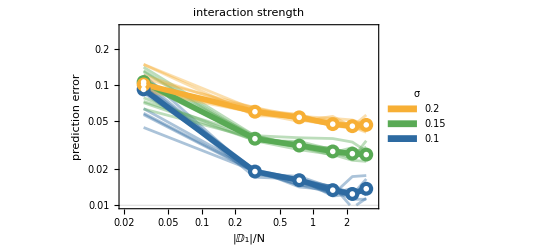

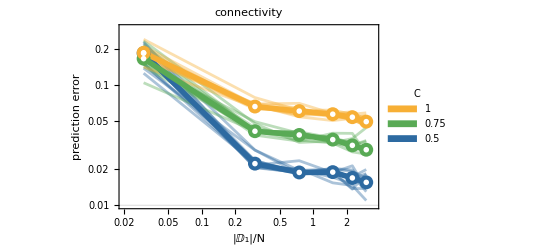

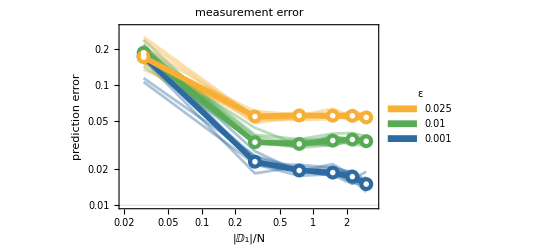

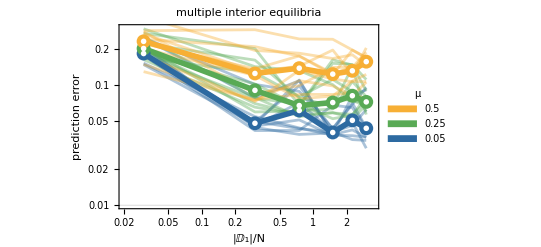

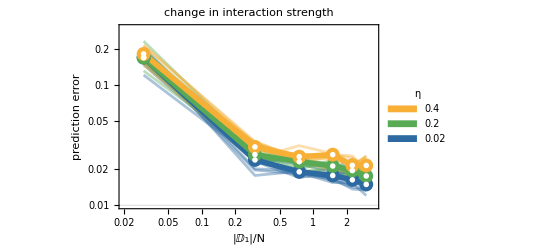

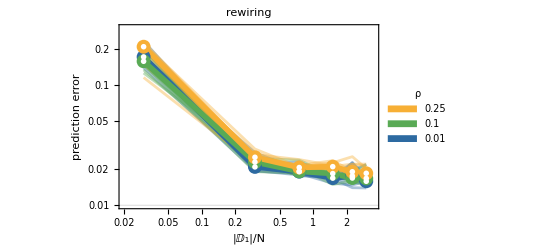

```mathematica
percentagesPlot[sTst,σ,"σ","interaction strength"]
percentagesPlot[cTst,Cn,"C","connectivity"]
percentagesPlot[nTst,ϵ,"ε","measurement error"]
percentagesPlot[mTst,μ,"μ","multiple interior equilibria"]
percentagesPlot[uTst,η,"η","change in interaction strength"]
percentagesPlot[rTst,ρ,"ρ","rewiring"]
```